```mathematica
γ[β_]:=1/(√(1-β^2))
```

```mathematica
P[μ_,β_]:=1/(γ[β]^4(1-β μ)^4);
```

```mathematica
Plot[P[μ,0.5],{μ,0,1}];
```

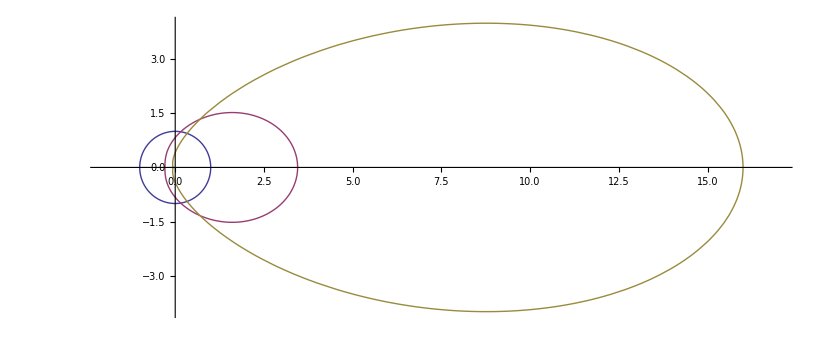

```mathematica
PolarPlot[{P[Cos[θ],0.0],P[Cos[θ],0.3],P[Cos[θ],0.6]},{θ,0,2π},PlotRange->{{-2,17},{-4,4}}]
```

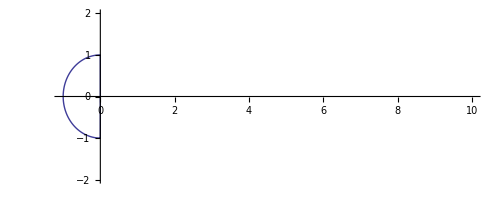

```mathematica
Pn[μ_,β_]:=If[μ<0,1/(γ[β]^4(1-β μ)^4),0]
PolarPlot[{Pn[Cos[θ],0.]},{θ,0,2π},PlotRange->{{-1,10},{-2,2}}]
```

```mathematica
LD[μ_]:=μ(1+1.5μ); (* limb darkening *)
```

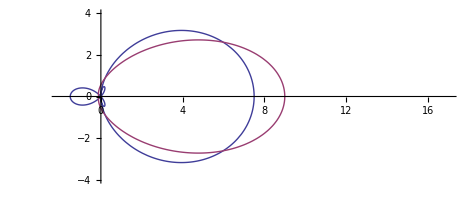

```mathematica
PolarPlot[{3LD[Cos[θ]],P[Cos[θ],0.5]},{θ,0,2π},PlotRange->{{-2,17},{-4,4}}]
```

```mathematica
γ[β_]:=1/(√(1-β^2))
```

```mathematica
∫_-1^1 1/(γ[β]^4(1-β μ)^4)μ^2 ⅆμ
```

ConditionalExpression[-(2 (1+3 β^2))/(3 (-1+β^2)),-1≤Re[β]≤1||β∉Reals]

```mathematica
∫_-1^1 1/(γ[β]^4(1-β μ)^4)μⅆμ
```

ConditionalExpression[-(8 β)/(3 (-1+β^2)),-1≤Re[β]≤1||β∉Reals]

```mathematica
∫_-1^1 1/(γ[β]^4(1-β μ)^4)ⅆμ
```

ConditionalExpression[-(2 (3+β^2))/(3 (-1+β^2)),-1≤Re[β]≤1||β∉Reals]

```mathematica
(-(8 β)/(3 (-1+β^2)))/(-(2 (3+β^2))/(3 (-1+β^2)))
```

(4 β)/(3+β^2)

```mathematica
(-(2 (1+3 β^2))/(3 (-1+β^2)))/(-(2 (3+β^2))/(3 (-1+β^2)))
```

(1+3 β^2)/(3+β^2)

```mathematica
(3+4(4 β)/(3+β^2)(4 β)/(3+β^2))/(5+2 √(4-3(4 β)/(3+β^2)(4 β)/(3+β^2)))//Simplify 1/(γ[β]^4(1-β μ)^4)
```

(3+(64 β^2)/((3+β^2)^2))/(5+4 √(((-3+β^2)^2)/((3+β^2)^2)))

```mathematica
(3+(64 β^2)/((3+β^2)^2))/(5+4 (3-β^2)/(3+β^2))//Simplify
```

(1+3 β^2)/(3+β^2)